```mathematica
ClearAll["Global`*"]
```

```mathematica
Clear[vv]
```

```mathematica
hh
```

hh

## Step 1. Load the bistatic scattering program- IEMM

```mathematica
Off[General::"spell1"];(Off[General::"spell"];)
BeginPackage["IEMM`"];
IEMM::"usage"="Calculates Bistatic Single surface scattering";
Begin["`private`"];
IEMM[fr_,sig_,corr_,theta_,ths_,phs_,er_,sp_,xx_]:=Module[{},
k=(2.0 π fr)/30.0;phi=0.0;σ=sig;L=corr;μr=1;thetas=ths;
ks=k sig;kL=k*corr;

s=N[Sin[(theta+0.01) Degree]];
cs=N[Cos[(theta+0.01) Degree]];
sf=N[Sin[phi Degree]];
cf=N[Cos[phi Degree]];

ss=N[Sin[ths Degree]];s2=s*s;
css=N[Cos[ths Degree]];
cfs=N[Cos[phs Degree]];
sfs=N[Sin[phs Degree]];

  kx=N[k s cf];       ky=N[k s sf];      kz=N[k cs];
ksx=N[k ss cfs];ksy=N[k ss sfs];ksz=N[k css];

rt=√(er-s^2);Rvi=N[(er cs-rt)/(er cs+rt)];Rhi=N[(cs-rt)/(cs+rt)];


wvnb=k √((ss cfs-s cf)^2+(ss sfs- s sf)^2);
TS=1;error=10^8;While[error>1/10^8,TS=TS+1;error=((ks^2 (cs+css)^2)^TS)/(TS!);];
spctrm=Switch[sp,
			           1,Do[ w[n]=N[L^2/n^2 (1+((wvnb L)/n)^2)^-1.5],{n,1,TS,1}],
				2,Do[ w[n]=N[L^2/(2 n) Exp[-(wvnb L)^2/(4 n)]],{n,1,TS,1}],
3,Do[ w[n]=If[wvnb==0,L^2/(3 n-2),N[(L^2 (wvnb L)^(xx n-1) BesselK[-xx n+1,wvnb L])/(2^(xx n-1) Gamma[xx n])]],{n,1,TS,1}],	
4,Do[ w[n]=  L^2/n^(2/xx)*NIntegrate[Exp[-(Abs[z])^xx]*BesselJ[0,z*wvnb L*(1/n^(1/xx))]*z,{z,0,9}],{n,1,TS,1}],
5,Do[ w[n]=N[∑_(m=0)^(TS+5) L^2 n^m/(m!) (xx/(n xx+m L))^(m+2)  Gamma[2+m] Hypergeometric2F1[(2+m)/2,(3+m)/2,1,-((xx  wvnb L)/(n xx+m L))^2]],{n,1,TS,1}]   ];

(*Compute R-transition*)
Rv0=N[(er -√er)/(er +√er)];Rh0=-Rv0;	Ft=8  Rv0^2 s*s( (cs+√(er-s^2))/(cs √(er-s^2)));
	
St=(0.25*Abs[Ft]^2 ∑_(n=1)^TS (ks cs)^(2 n)/(n!)w[n])/(∑_(n=1)^TS (ks cs)^(2 n)/(n!)Abs[Ft/2+2^(n+1)Rv0/cs Exp[-(ks cs)^2]]^2 w[n]);


(*there is really no difference between Stv and Sth !  St0= Stv when n=1 and ks-> 0. We drop v or h *)


(*S0=(0.25 ks cs Abs[Fvv]^2 w[n])/(ks cs Abs[Fvv/2+2^(n+1)Rv0/cs Exp[-(ks cs)^2]]^2 w[n])=(0.25 Abs[Fvv]^2)/Abs[Fvv/2+4 Rv0/cs]^2=Abs[Fvv]^2/Abs[Fvv+8 Rv0/cs]^2 has no polarization dependence*)

St0=1/Abs[1+8 Rv0/(cs *Ft)]^2;
Tf=1-St/St0;

Rtv=Rvi +(Rv0-Rvi)Tf;
Rth=Rhi +(Rh0-Rhi)Tf;

(*Rtv, Rth are needed for frequency behavior calculation
		
	A=(cs+Zx*s);
	B=er*(1+Zx^2+Zy^2);
	CC=s^2-2*Zx*s*cs+Zx^2*cs^2+Zy^2;
	
	Rh=(A-√(B-CC))/(A+√(B-CC)); Rv=(er*A-√(B-CC))/(er*A+√(B-CC));
	
σx=1.1*sig/L;σy=σx;
	pd=Exp[-Zx^2/(2*σx^2)-Zy^2/(2*σy^2)];
	Ra=1/(2*π*σx*σy)*NIntegrate[{Rv*pd,Rh*pd},{Zx,-3*σx,0,3*σx},{Zy,-3*σy,0,3*σy}];
			
		
 fvv=((2  Ra[[1]]) (s ss-(1+cs css) cfs))/(cs+css);fhh=-((2 Ra[[2]]) (s ss-(1+cs css) cfs))/(cs+css);*)
	(* Average reflection coefficients, Ra[[1]] and Ra[[2]], are to correct scattering near the Brewster angle*)

fvv=N[1/(cs+css)( (2 Rtv) (s ss-(cs css+1) cfs))]; 
fhh=N[-1/(cs+css)((2 Rth) (s ss-(cs css+1) cfs))];



(*There are 4 F-coefficients:up-down (ud)and incident-scatter (is) *)
		 F[ud_,is_]:=Module[{vv,hh,c11,c21,c31,c41,c51,c61,c12,c22,c32,c42,c52,c62,q,qt},
				If[is==1,{
Gqi=ud kz; (* Gqi will switch to Gqti, when Ci1 changes to Ci2. This applies to C2i, C3i, C5i*)  Gqti=ud k √(er-s^2);qi=ud kz;

c11=k cfs (ksz-qi);
c21= cs (cfs(k^2 s cf (ss cfs-s cf)+  Gqi (k css-qi))+ k^2 cf s ss  sfs^2);c31= k s(s cf cfs(k css-qi) -Gqi (cfs (ss cfs-s cf) + ss sfs^2));
c41=k cs (cfs  css (k css-qi)+k ss(ss cfs-s cf));
c51=Gqi (cfs css (qi-k css)-k ss(ss cfs-s cf));

c12=k cfs  (ksz-qi);
c22=cs (cfs(k^2 s cf(ss cfs-s cf)+  Gqti (k css-qi))+ k^2 cf s ss  sfs^2);
c32= k s(s cf cfs(k css-qi) -Gqti (cfs (ss cfs-s cf) - ss sfs^2));
c42=k cs (cfs  css (k css-qi)+k ss(ss cfs-s cf));
c52=Gqti (cfs css (qi-k css)-k ss(ss cfs-s cf));

}
						];
				
        If[is==2,{
Gqs=ud ksz; qs=ud ksz;Gqts=ud k √(er-ss^2);
						c11=cfs k (kz+qs);
						c21=Gqs (cfs (cs (k cs+qs)-k s(ss cfs-s cf))-k s ss sfs^2);
						c31= k ss(k cs(ss cfs-s cf)+ s(kz+qs) );
						c41=k css(cfs(cs (kz+qs)-k s(ss cfs-s cf) )-k s ss sfs^2);
						c51=-css ( k^2 ss  (ss cfs-s cf)+Gqs cfs(kz+qs));
						
						c12=cfs k (kz+qs);
						c22=Gqts (cfs (cs (kz+qs)-k s(ss cfs-s cf))-k s ss sfs^2);
						c32= k ss(k cs(ss cfs-s cf)+ s(kz+qs) );
						c42=k css(cfs(cs (kz+qs)-k s(ss cfs-s cf) )-k s ss sfs^2);
						c52=-css ( k^2 ss  (ss cfs-s cf)+Gqts cfs(kz+qs));
					}
						]; 
q=kz;qt=k √(er-s^2);
vv=(1+Rvi) (-1/q((1-Rvi)c11)+((1+Rvi)c12)/qt)+
						(1-Rvi) (((1-Rvi)c21)/q-((1+Rvi)c22)/qt)+
						(1+Rvi) (((1-Rvi)c31)/q-((1+Rvi)c32)/(er qt))+
						(1-Rvi)(((1+Rvi)c41)/q-1/qt(er(1-Rvi)c42))+
						(1+Rvi) (((1+Rvi)c51)/q-((1-Rvi)c52)/qt);
hh= (1+Rhi) (((1-Rhi)c11)/q-1/qt(er (1+Rhi)c12))-
						(1-Rhi) (((1-Rhi)c21)/q-((1+Rhi)c22)/qt)-
						(1+Rhi) (((1-Rhi)c31)/q-((1+Rhi)c32)/qt)-
						(1-Rhi) (((1+Rhi)c41)/q-((1-Rhi)c42)/qt)-
						(1+Rhi) (((1+Rhi)c51)/q-((1-Rhi)c52)/qt);
Return[{vv,hh}];
];

Fvvupi=F[+1,1]⟦1⟧;Fhhupi=F[+1,1]⟦2⟧;
Fvvdni=F[-1,1]⟦1⟧;Fhhdni=F[-1,1]⟦2⟧;
Fvvups=F[+1,2]⟦1⟧;Fhhups=F[+1,2]⟦2⟧;
Fvvdns=F[-1,2]⟦1⟧;Fhhdns=F[-1,2]⟦2⟧;
		
aav=1/2 k^2 Abs[fvv]^2 Exp[-ks^2 (cs+css)^2] ∑_(n=1)^TS 1/(n!)((ks^2 (cs+css)^2)^n w[n]);
aah=1/2 k^2 Abs[fhh]^2 Exp[-ks^2 (cs+css)^2] ∑_(n=1)^TS 1/(n!)((ks^2 (cs+css)^2)^n w[n]);
kv=10 Log[10,N[aav]];
kh=10 Log[10,N[aah]];
qi=k cs;qs=k css;
(*Do[Ivv[n]=(kz+ksz)^n fvv Exp[-σ^2kz ksz]+
					1/4(Fvvupi (ksz-qi)^(n-1)Exp[-σ^2(qi^2-qi(ksz-kz))]+
								Fvvdni (ksz+qi)^(n-1)Exp[-σ^2(qi^2+qi(ksz-kz))]+
								Fvvups (kz+qs)^(n-1)Exp[-σ^2(qs^2-qs(ksz-kz))]+
								Fvvdns (kz-qs)^(n-1)Exp[-σ^2(qs^2+qs(ksz-kz))]),{n,1,TS,1}];
	
		
Do[Ihh[n]=(kz+ksz)^n fhh Exp[-σ^2kz ksz]+
					1/4(Fhhupi (ksz-qi)^(n-1)Exp[-σ^2(qi^2-qi(ksz-kz))]+
								Fhhdni (ksz+qi)^(n-1)Exp[-σ^2(qi^2+qi(ksz-kz))]+
								Fhhups (kz+qs)^(n-1)Exp[-σ^2(qs^2-qs(ksz-kz))]+
								Fhhdns (kz-qs)^(n-1)Exp[-σ^2(qs^2+qs(ksz-kz))]),{n,1,TS,1}];*)
Ivv=(kz+ksz)^n fvv Exp[-σ^2 kz ksz]+
					1/4(Fvvupi (ksz-qi)^(n-1)Exp[-σ^2(qi^2-qi(ksz-kz))]+
								Fvvdni (ksz+qi)^(n-1)Exp[-σ^2(qi^2+qi(ksz-kz))]+
								Fvvups (kz+qs)^(n-1)Exp[-σ^2(qs^2-qs(ksz-kz))]+
								Fvvdns (kz-qs)^(n-1)Exp[-σ^2(qs^2+qs(ksz-kz))]);
Ihh=(kz+ksz)^n fhh Exp[-σ^2 kz ksz]+
					1/4(Fhhupi (ksz-qi)^(n-1)Exp[-σ^2(qi^2-qi(ksz-kz))]+
								Fhhdni (ksz+qi)^(n-1)Exp[-σ^2(qi^2+qi(ksz-kz))]+
								Fhhups (kz+qs)^(n-1)Exp[-σ^2(qs^2-qs(ksz-kz))]+
								Fhhdns (kz-qs)^(n-1)Exp[-σ^2(qs^2+qs(ksz-kz))]);

(*ct=N[Cot[theta Degree]];
cts=N[Cot[thetas Degree]];
rslp=Switch[sp,
						1,√1 sig/L,
						2,√2 sig/L,
						3,If[xx==1.5,√3 sig/L,0],
						4,√1 sig/L,
						5,√2 sig/(√(xx* L))];
If[UnsameQ[rslp,0],
ctorslp=ct/(√2 rslp);
ctsorslp=cts/(√2 rslp);
shadf=1/2(1/(√π ctorslp)Exp[-ctorslp^2]-Erfc[ctorslp]);
shadfs=1/2(1/(√π ctsorslp)Exp[-ctsorslp^2]-Erfc[ctsorslp]);
ShdwS=N[1/(1+shadf+shadfs)];
ShdwS=1;
Print["Warning: RMS surface slope not available. Shadowing not used."]]; *)
ShdwS=1;
iemmvv=ShdwS k^2/2 Exp[-σ^2(kz^2+ksz^2)]∑_(n=1)^TS σ^(2n)Abs[Ivv]^2 w[n]/(n!);
iemmhh=ShdwS k^2/2 Exp[-σ^2(kz^2+ksz^2)]∑_(n=1)^TS σ^(2n)Abs[Ihh]^2 w[n]/(n!);
ssv=10 Log[10,N[iemmvv]];
ssh=10 Log[10,N[iemmhh]];
(*Compute the old IEM*)
sq=√(μr er-s^2);sqs=√(μr er-ss^2);rcs=(css sq)/(cs sqs);
Fvv=((μr er-s^2-er cs^2)(1+Rvi)^2)/((er cs)^2 css)s(ss-s cfs);Fhh=-((μr er-s^2-μr cs^2)(1+Rhi)^2)/((μr cs)^2 css)s(ss-s cfs);
Fvs=(1-Rvi^2)((1/rcs-1)css cfs +1/cs((1-rcs)(cfs-s ss))+1/sq((er-rcs) ss(s-ss cfs)));
Fhs=-(1-Rhi^2)((1/rcs-1)css cfs +1/cs((1-rcs)(cfs-s ss))+1/sq((μr-rcs) ss(s-ss cfs)));
oIvv=(kz+ksz)^n fvv Exp[-σ^2 kz ksz]+(ksz^n Fvv+kz^n Fvs)/2;
oIhh=(kz+ksz)^n fhh Exp[-σ^2 kz ksz]+(ksz^n Fhh+kz^n Fhs)/2;
iemvv=ShdwS k^2/2 Exp[-σ^2(kz^2+ksz^2)]∑_(n=1)^TS σ^(2n)Abs[oIvv]^2 w[n]/(n!);
iemhh=ShdwS k^2/2 Exp[-σ^2(kz^2+ksz^2)]∑_(n=1)^TS σ^(2n)Abs[oIhh]^2 w[n]/(n!);

sov=10 Log[10,N[iemvv]];
soh=10 Log[10,N[iemhh]];

Return[{ths,iemmvv,iemmhh,sov,soh}];]
End[];EndPackage[]
```

```mathematica
(*IIEMB[fr_,sig_,corr_,theta_,ths_,phs_,er_,sp_,xx_]*)
```

```mathematica
Do[otp=IEMM[4.775,0.2,1.0,theta,theta,180,62,2,1.5];Print[otp], {theta, 10,40,10}];
```

{10,0.087263,0.0788899,-10.5796,-11.0434}

{20,0.0924912,0.0625237,-10.2994,-12.0932}

{30,0.0984641,0.0422832,-10.0037,-13.8592}

{40,0.101758,0.0241673,-9.853,-16.3879}

```mathematica
(1) This is the Rayleigh layer model.It consists of a top surface scattering term,a bottom surface scattering term,a layer volume scattering term and an interaction term.(2) Exact calculation should use the real angle of transmision given in the program below.er=relative complex dielectric constant of the layer;
erb=relative complex dielectric constant of the half-space below the layer;
```

## Step 2. Load graphics package

```mathematica
Needs["Graphics`MultipleListPlot`"];
sym1=PlotSymbol[Diamond,3];
sym2=PlotSymbol[Triangle,5];
sym3=PlotSymbol[Star,2];
sym4=PlotSymbol[Box,3];
```

## Step 3. Load the Rayleigh Layer Scattering Program (1) This is the Rayleigh layer model. It consists of a top surface scattering term, a bottom surface scattering term, a layer volume scattering term and an interaction term. (2) Exact calculation should use the real angle of transmision given in the program below. er = relative complex dielectric constant of the layer; erb=relative complex dielectric constant of the half-space below the layer;

```mathematica
Off[General::"spell1"];Off[General::"spell"];
BeginPackage["Rlay`",{"IEMM`","Graphics`MultipleListPlot`"}];
Rlay::"usage"="Calculates Layer volume-surf scattering and interaction";
Begin["`private`"];
Rlay[fr_,al_,tau_,theta_,thetas_,phs_,er_,erb_,sig1_,sig2_,L1_,L2_,sp_]:=Module[{},
	k=(2.0 Pi fr)/30.0;kl=k √Re[er];
	
		cs=N[Cos[theta Degree]];
		s=N[Sin[theta Degree]];
		s2=s^2;
		cfs=N[Cos[phs Degree]];
		sfs=N[Sin[phs Degree]];
		css=N[Cos[thetas Degree]];
		ss=N[Sin[thetas Degree]];
		ss2=ss^2;
(* Calculations of sine and cosine using real-thetat and real-thetao*)
alf=Im[√er]//N; be=Re[√er]; p=2 alf* be; q=be^2-alf^2-s2;qs=be^2-alf^2-ss2;
tant=1.414 s/√(q+√(p^2+q^2)); thetat=ArcTan[tant]*180/π; st=Sin[thetat Degree]//N;cst=√(1-st^2);
tano=1.414 ss/√(q+√(p^2+qs^2)); thetao=ArcTan[tano]*180/π; so=Sin[thetao Degree]//N;cso=√(1-so^2);
  
(*Top boundary & bottom reflectivity & transmissivity*)
		rt=√(er-s^2);rvi=N[(er cs-rt)/(er cs+rt)];rhi=N[(cs-rt)/(cs+rt)];Rv=Abs[rvi]^2;Rh=Abs[rhi]^2;
	rts=√(er-ss^2);rvs=N[(er css-rts)/(er css+rts)];rhs=N[(css-rts)/(css+rts)];Rvs=Abs[rvs]^2;Rhs=Abs[rhs]^2;

rtbt=√(erb/er-st^2);rvt=N[((erb/er) cst-rtbt)/((erb/er) cst+rtbt)];rht=N[(cst-rtbt)/(cst+rtbt)];Rvt=Abs[rvt]^2;Rht=Abs[rht]^2;
rtbo=√(erb/er-so^2);rvo=N[((erb/er) cso-rtbo)/((erb/er) cso+rtbo)];rho=N[(cso-rtbo)/(cso+rtbo)];Rvo=Abs[rvo]^2;Rho=Abs[rho]^2;
Tv=1-Rv; Th=1-Rh;
Tvs=1-Rvs; Ths=1-Rhs;
(*Tv=1;Th=1;*)
(*Tvs=1;Ths=1;*)
(*Tvs=1-Rvs; Ths=1-Rhs; *)(*for test by Fei Zhao*)

(*Rayleigh Phase functions and the volume scattering terms. Due to difference in definition in Chandrasekar where phs =0 means the TR are together and phs=180 means TR are 180 apart, to use spherical coordinate in defining Phs, we need to add 180 to phs*)

phh=0.75(1+Cos[2 phs Degree]);
pvv=0.75(2  st^2 so^2+cst^2 cso^2(1+Cos[2 phs Degree])+4 cst cso st so Cos[( phs+180) Degree]);
pvvf=0.75(2  st^2 so^2+cst^2 cso^2(1+Cos[2*0 Degree])-4 cst cso st so );

volvv=css cst Tv Tvs al (1-Exp[-(tau(cso+cst))/(cso cst)])pvv/(cso+cst);
volhh=css cst Th Ths al (1-Exp[-(tau(cso+cst))/(cso cst)])phh/(cso+cst);
(*volvv = Tv * Tvs;*)
(*volhh =Th * Ths;*)

(*Interaction terms*)

If[cso≠cst,
invv=css  Tv  Tvs al((Exp[-tau/cso]-Exp[-tau/cst])/(cso-cst))Exp[-kl^2 sig2^2(cso+cst)^2]pvvf(cso Rvo Exp[-tau/cso]+cst Rvt Exp[-tau/cst]),invv=2 cs Tv^2 al (tau/cst)(Exp[-kl^2 sig2^2(cso+cst)^2] Rvt) pvvf  Exp[-2tau/cst]];

If[cso≠cst,
inhh=css  Th  Ths al((Exp[-tau/cso]-Exp[-tau/cst])/(cso-cst))Exp[-kl^2 sig2^2(cso+cst)^2]phh(cso Rho Exp[-tau/cso]+cst Rht Exp[-tau/cst]),inhh=2 cs Th^2 al (tau/cst)(Exp[-kl^2 sig2^2(cso+cst)^2] Rht) phh Exp[-2tau/cst]];

(*Calculate surface scattering from TOP & BOTTOM boundaries. Call IEMM*)

stop=IEMM[fr,sig1,L1,theta,thetas,phs,er,1,1.5];
stopv=stop[[2]];
stoph=stop[[3]];
  (*ebr=Re[erb/er]; *)(*其实erb在传参数传进来时就已经被er归一化了，因此不需要再归一化*)
ebr=erb;
sbot=IEMM[fr,sig2,L2,thetat,thetao,phs,ebr,1,1.5];
cov=css  Tv Tvs Exp[-tau(1/cso+1/cst)]/cst;
coh=css  Th Ths Exp[-tau(1/cso+1/cst)]/cst;
sbotv=cov*sbot[[2]];
sboth=coh*sbot[[3]];

ssv=volvv+invv+stopv+sbotv;(*Print[{stopv, sbotv}];*)
ssh=volhh+inhh+stoph+sboth;
Rlvv=10.0Log[10.,ssv];vv=10.0Log[10.,volvv];vint=10.0Log[10.,invv];stvv=10.0Log[10.,stopv];sbvv=10.0Log[10.,sbotv];
Rlhh=10.0Log[10.,ssh];hh=10.0Log[10.,volhh];hint=10.0Log[10.,inhh];sthh=10.0Log[10.,stoph];sbhh=10.0Log[10.,sboth];

Return[{thetas,Rlvv,Rlhh,vv, hh, vint,hint,stvv,sthh,sbvv,sbhh, cov,coh}];];
End[];EndPackage[];
```

Get::noopen: 无法打开 Graphics`MultipleListPlot`.

Needs::nocont: 当运行  Needs 时，没有创建上下文 Graphics`MultipleListPlot`.

```mathematica
fr=10;  al=0.42;tau=0.75; phs=180;
theta=thetas;er=2.1-I 0.002;erb=2.65-I 0.008; sig1=.25;sig2=0.39; L1=5.79; L2=3.4;sp=1;

start=10.01;end=70.01;step=5;

outp=Table[Rlay[fr,al,tau,theta,thetas,phs,er,erb/er,sig1,sig2,L1,L2,sp],{thetas,start,end,step}];
vv=Map[{#[[1]],#[[2]]}&,outp];
hh=Map[{#[[1]],#[[3]]}&,outp];
vov=Map[{#[[1]],#[[4]]}&,outp];
voh=Map[{#[[1]],#[[5]]}&,outp];
inv=Map[{#[[1]],#[[6]]}&,outp];
inh=Map[{#[[1]],#[[7]]}&,outp];
stv=Map[{#[[1]],#[[8]]}&,outp];
sth=Map[{#[[1]],#[[9]]}&,outp];
sbv=Map[{#[[1]],#[[10]]}&,outp];
sbh=Map[{#[[1]],#[[11]]}&,outp];
cov=Map[{#[[1]],#[[12]]}&,outp];
coh=Map[{#[[1]],#[[13]]}&,outp];

Needs["Statistics`DataManipulation`"];


Print[TableForm[{vv},TableHeadings->{{"VV σ^0"},{"Layer"}}]];
Print[TableForm[{hh},TableHeadings->{{"HH σ^0"},{"Layer"}}]];
Null
```

```mathematica
ListPlot[vov, Joined->True]
```

## Step 4 (a). Compute backscattering from a Rayleigh layer with irregular boundaries----Fig 8.10 (a)

```mathematica
fr=17;  al=0.96;tau=0.3; phs=180;
theta=thetas;er=1.6-I 0.001;erb=5;sig1=.1;sig2=0.5; L1=1.2; L2=20.0;sp=1;


start=10.010;end=80.01;step=5;

outp=Table[Rlay[fr,al,tau,theta,thetas,phs,er,erb/er,sig1,sig2,L1,L2,sp],{thetas,start,end,step}];
vv=Map[{#[[1]],#[[2]]}&,outp];
hh=Map[{#[[1]],#[[3]]}&,outp];
vov=Map[{#[[1]],#[[4]]}&,outp];
voh=Map[{#[[1]],#[[5]]}&,outp];
inv=Map[{#[[1]],#[[6]]}&,outp];
inh=Map[{#[[1]],#[[7]]}&,outp];
stv=Map[{#[[1]],#[[8]]}&,outp];
sth=Map[{#[[1]],#[[9]]}&,outp];
sbv=Map[{#[[1]],#[[10]]}&,outp];
sbh=Map[{#[[1]],#[[11]]}&,outp];

Needs["Statistics`DataManipulation`"];
Needs["Graphics`MultipleListPlot`"];

Print[TableForm[{vv,vov,inv,stv,sbv},TableHeadings->{{"VV σ^0"},{"Layer"}}]];
Print[TableForm[{hh,voh,inh,sth,sbh},TableHeadings->{{"HH σ^0"},{"Layer"}}]];
```

Get::noopen: 无法打开 Statistics`DataManipulation`.

Needs::nocont: 当运行  Needs 时，没有创建上下文 Statistics`DataManipulation`.

Get::noopen: 无法打开 Graphics`MultipleListPlot`.

Needs::nocont: 当运行  Needs 时，没有创建上下文 Graphics`MultipleListPlot`.

| Layer |  |  |  |  |  |  |  |  |  |  |  |  |  | 
VV σ^0 | 10.01
-3.06707 | 15.01
-4.13093 | 20.01
-4.61512 | 25.01
-4.88962 | 30.01
-5.09263 | 35.01
-5.28097 | 40.01
-5.48407 | 45.01
-5.72336 | 50.01
-6.02102 | 55.01
-6.40646 | 60.01
-6.92461 | 65.01
-7.65074 | 70.01
-8.72201 | 75.01
-10.4154 | 80.01
-13.3889
 | 10.01
-5.03338 | 15.01
-5.07276 | 20.01
-5.13013 | 25.01
-5.20797 | 30.01
-5.30995 | 35.01
-5.44138 | 40.01
-5.60989 | 45.01
-5.82676 | 50.01
-6.10901 | 55.01
-6.4832 | 60.01
-6.99263 | 65.01
-7.71162 | 70.01
-8.77686 | 75.01
-10.4654 | 80.01
-13.4362
 | 10.01
-105.892 | 15.01
-104.5 | 20.01
-102.665 | 25.01
-100.503 | 30.01
-98.1617 | 35.01
-95.8301 | 40.01
-93.7448 | 45.01
-92.217 | 50.01
-91.7038 | 55.01
-93.053 | 60.01
-98.9694 | 65.01
-104.971 | 70.01
-93.0898 | 75.01
-90.5125 | 80.01
-92.0991
 | 10.01
-14.8597 | 15.01
-18.3788 | 20.01
-21.1312 | 25.01
-23.3256 | 30.01
-25.1186 | 35.01
-26.6231 | 40.01
-27.9282 | 45.01
-29.1124 | 50.01
-30.2538 | 55.01
-31.4407 | 60.01
-32.7853 | 65.01
-34.4425 | 70.01
-36.6285 | 75.01
-39.563 | 80.01
-42.8999
 | 10.01
-8.32566 | 15.01
-12.162 | 20.01
-15.096 | 25.01
-17.3811 | 30.01
-19.1966 | 35.01
-20.6689 | 40.01
-21.8933 | 45.01
-22.948 | 50.01
-23.9034 | 55.01
-24.8293 | 60.01
-25.8027 | 65.01
-26.9217 | 70.01
-28.3348 | 75.01
-30.3186 | 80.01
-33.5206

| Layer |  |  |  |  |  |  |  |  |  |  |  |  |  | 
HH σ^0 | 10.01
-3.17244 | 15.01
-4.26808 | 20.01
-4.77123 | 25.01
-5.06763 | 30.01
-5.30197 | 35.01
-5.53439 | 40.01
-5.79733 | 45.01
-6.11602 | 50.01
-6.51791 | 55.01
-7.03981 | 60.01
-7.73703 | 65.01
-8.69936 | 70.01
-10.084 | 75.01
-12.1953 | 80.01
-15.7272
 | 10.01
-5.04518 | 15.01
-5.09979 | 20.01
-5.17943 | 25.01
-5.28766 | 30.01
-5.42967 | 35.01
-5.61286 | 40.01
-5.84781 | 45.01
-6.14981 | 50.01
-6.54141 | 55.01
-7.05685 | 60.01
-7.75001 | 65.01
-8.70995 | 70.01
-10.0936 | 75.01
-12.2058 | 80.01
-15.7431
 | 10.01
-105.332 | 15.01
-103.228 | 20.01
-100.376 | 25.01
-96.8658 | 30.01
-92.8082 | 35.01
-88.3349 | 40.01
-83.5944 | 45.01
-78.7504 | 50.01
-73.9797 | 55.01
-69.473 | 60.01
-65.438 | 65.01
-62.1102 | 70.01
-59.7814 | 75.01
-58.8744 | 80.01
-60.183
 | 10.01
-14.9268 | 15.01
-18.5918 | 20.01
-21.5784 | 25.01
-24.0803 | 30.01
-26.2352 | 35.01
-28.1356 | 40.01
-29.8485 | 45.01
-31.4274 | 50.01
-32.9199 | 55.01
-34.3712 | 60.01
-35.819 | 65.01
-37.2704 | 70.01
-38.6534 | 75.01
-39.8204 | 80.01
-40.9243
 | 10.01
-8.64669 | 15.01
-12.8902 | 20.01
-16.3921 | 25.01
-19.4032 | 30.01
-22.0982 | 35.01
-24.5956 | 40.01
-26.9769 | 45.01
-29.2982 | 50.01
-31.595 | 55.01
-33.887 | 60.01
-36.1872 | 65.01
-38.5269 | 70.01
-41.009 | 75.01
-43.9133 | 80.01
-47.9551

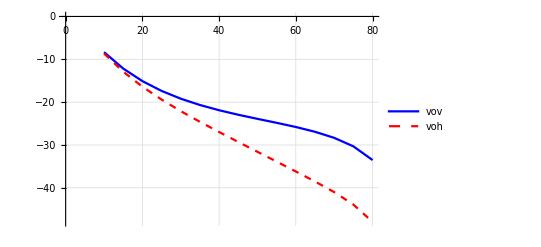

```mathematica
ListPlot[{sbv,sbh}, Joined->True, GridLines->Automatic, PlotLegends->{"vov", "voh"},PlotStyle->{{Thick,Blue},{Dashed,Red}}]
```

```mathematica
vov
```

{{10.01,-5.03338},{15.01,-5.07276},{20.01,-5.13013},{25.01,-5.20797},{30.01,-5.30995},{35.01,-5.44138},{40.01,-5.60989},{45.01,-5.82676},{50.01,-6.10901},{55.01,-6.4832},{60.01,-6.99263},{65.01,-7.71162},{70.01,-8.77686},{75.01,-10.4654},{80.01,-13.4362}}

## Step 5 (a). Load plotting program and Data from dry snow-----Fig 8.10 (a)

```mathematica
dav={{{10,-2},ErrorBar[0.5]},{{20,-5.},ErrorBar[0.5]},{{30,-5.7},ErrorBar[0.5]},{{40,-6.3},ErrorBar[0.5]},{{50,-7.0},ErrorBar[0.5]},{{60,-7.5},ErrorBar[0.5]},{{70,-9.1},ErrorBar[0.5]},{{80,-14},ErrorBar[0.5]}};

dah={{{10,-2},ErrorBar[0.5]},{{20,-5.},ErrorBar[0.5]},{{30,-5.7},ErrorBar[0.5]},{{40,-6.3},ErrorBar[0.5]},{{50,-7.0},ErrorBar[0.5]},{{60,-7.5},ErrorBar[0.5]},{{70,-9.1},ErrorBar[0.5]},{{80,-14},ErrorBar[0.5]}};

g1=Graphics[MultipleListPlot[vv,hh,dav,dah,
	PlotStyle->{Dashing[{0.03,0.03}],Dashing[{0.01,0.01}],{Hue[.85]},{Hue[.3]},{Hue[0.5]},{Hue[0.1]}},
	AspectRatio->1,
	PlotLegend->{FontForm["vv",{"Arial",14}],FontForm["hh",{"Arial",14}],FontForm["dav",{"Arial",14}],FontForm["dah",{"Arial",14}],FontForm["vIEM",{"Arial",14}],FontForm["hIEM",{"Arial",14}]},
	PlotRange->{-20,5},DisplayFunction->Identity,
	SymbolShape->{MakeSymbol[RegularPolygon[5,0]],MakeSymbol[RegularPolygon[4,0]],PlotSymbol[Star,5],PlotSymbol[Diamond,5],MakeSymbol[RegularPolygon[3,0]],MakeSymbol[RegularPolygon[6,0]]},
		PlotLabel->FontForm["Scattering Coefficient",{"Arial",16}],Frame->True,Axes->False,
	PlotJoined->{True,True,False,False,True,True},FrameLabel->{FontForm["θ",{"Arial",18}],FontForm["σ^0",{"Arial",18}]},Background->GrayLevel[0.998],DefaultFont->14,GridLines->Automatic,RotateLabel->False]];
```

## Step 6 (a). Show plots --data from p. 879--vol.2 17 GHz-----Fig 8.10 (a)

```mathematica
Show[g1,DisplayFunction->$DisplayFunction];
```

```mathematica
Fig 8.10 (a)
```

## Step 4 (b). Compute backscattering from a Rayleigh layer with irregular boundaries----Fig 8.10 (b) using wet snow --data from p.877-----vol.2

```mathematica
fr=17;  al=0.17;tau=2.5; phs=180;
theta=thetas;er=1.7-I 0.005;erb=5;sig1=.1;sig2=0.5; L1=1.2; L2=20.0;sp=1;

start=10.010;end=70.01;step=5;

outp=Table[Rlay[fr,al,tau,theta,thetas,phs,er,erb/er,sig1,sig2,L1,L2,sp],{thetas,start,end,step}];
vv=Map[{#[[1]],#[[2]]}&,outp];
hh=Map[{#[[1]],#[[3]]}&,outp];
vov=Map[{#[[1]],#[[4]]}&,outp];
voh=Map[{#[[1]],#[[5]]}&,outp];
inv=Map[{#[[1]],#[[6]]}&,outp];
inh=Map[{#[[1]],#[[7]]}&,outp];
stv=Map[{#[[1]],#[[8]]}&,outp];
sth=Map[{#[[1]],#[[9]]}&,outp];
sbv=Map[{#[[1]],#[[10]]}&,outp];
sbh=Map[{#[[1]],#[[11]]}&,outp];

Needs["Statistics`DataManipulation`"];
Needs["Graphics`MultipleListPlot`"];

Print[TableForm[{vv,vov,inv,stv,sbv},TableHeadings->{{"VV σ^0"},{"Layer"}}]];
Print[TableForm[{hh,voh,inh,sth,sbh},TableHeadings->{{"HH σ^0"},{"Layer"}}]];
```

## Step 5 (b). Load plotting program and Data from wet snow----Fig 8.10 (b)

```mathematica
dav={{{10,-8},ErrorBar[0.5]},{{20,-9.},ErrorBar[0.5]},{{30,-9.5},ErrorBar[0.5]},{{40,-10},ErrorBar[0.5]},{{50,-10.7},ErrorBar[0.5]},{{60,-12.0},ErrorBar[0.5]},{{70,-14.5},ErrorBar[0.5]}};

dah={{{10,-8},ErrorBar[0.5]},{{20,-9.},ErrorBar[0.5]},{{30,-9.5},ErrorBar[0.5]},{{40,-10},ErrorBar[0.5]},{{50,-10.7},ErrorBar[0.5]},{{60,-12.0},ErrorBar[0.5]},{{70,-14.5},ErrorBar[0.5]}};

g1=Graphics[MultipleListPlot[vv,hh,dav,dah,
	PlotStyle->{Dashing[{0.03,0.03}],Dashing[{0.01,0.01}],{Hue[.85]},{Hue[.3]},{Hue[0.5]},{Hue[0.1]}},
	AspectRatio->1,
	PlotLegend->{FontForm["vv",{"Arial",14}],FontForm["hh",{"Arial",14}],FontForm["dav",{"Arial",14}],FontForm["dah",{"Arial",14}],FontForm["vIEM",{"Arial",14}],FontForm["hIEM",{"Arial",14}]},
	PlotRange->{-20,-5},DisplayFunction->Identity,
	SymbolShape->{MakeSymbol[RegularPolygon[5,0]],MakeSymbol[RegularPolygon[4,0]],PlotSymbol[Star,5],PlotSymbol[Diamond,5],MakeSymbol[RegularPolygon[3,0]],MakeSymbol[RegularPolygon[6,0]]},
		PlotLabel->FontForm["Scattering Coefficient",{"Arial",16}],Frame->True,Axes->False,
	PlotJoined->{True,True,False,False,True,True},FrameLabel->{FontForm["θ",{"Arial",18}],FontForm["σ^0",{"Arial",18}]},Background->GrayLevel[0.998],DefaultFont->14,GridLines->Automatic,RotateLabel->False]];
```

## Step 6 (b). Show plots ---data from p. 877--vol.2 17 GHz-----Fig 8.10 (b)

```mathematica
Show[g1,DisplayFunction->$DisplayFunction];
```

```mathematica
Fig 8.10 (b)
```